## Import paddock data

```mathematica
rawMetadata=Import["/Users/katjad/Documents/Github/SheepCapstone/Salt6_corners_food locations_collective decision making_March2019.csv"];
```

```mathematica
paddock=rawMetadata[[-4;;-1,-2;;-1]];
feeding=rawMetadata[[2;;11,-2;;-1]];
water=rawMetadata[[12,-2;;-1]];
```

```mathematica
paddockRegion=BoundaryDiscretizeGraphics[Polygon[paddock]];metadataGraphic=Graphics[{LightBrown,Polygon[paddock],Darker[Green],Circle[#,30]&/@feeding,Thick,Darker[Blue],Circle[water,50]}];
```

```mathematica
rawXs=Import["/Users/katjad/Documents/Github/SheepCapstone/xs.csv"];
rawYs=Import["/Users/katjad/Documents/Github/SheepCapstone/ys.csv"];
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv"];
rawTs=Import["/Users/katjad/Documents/Github/SheepCapstone/ts.csv"];
rawTsStart=Import["/Users/katjad/Documents/Github/SheepCapstone/period.start.idxs.csv"];
```

```mathematica
rawCoordinates=Table[{rawXs[[x,y]],rawYs[[x,y]]},{x,2,52},{y,2,210352}]/."NA"->Missing[];
```

```mathematica
rawCoordinates[[11,400]]
```

{580816.,6.56371×10^6}

## Group Membership results

```mathematica
FullStabilityGraph=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/FullStabilityGraph.mx"];
```

```mathematica
mergingEvents =Select[VertexList[FullStabilityGraph],VertexInDegree[FullStabilityGraph,#]≥2&]
```

{{{2,3,4,5,7,11,14,16,17,20,22,23,26,27,29,33,36,38,39,40,47},18},8247,{{1,4,9,16,20,39,43},210339}}
 |  |  |  |

```mathematica
splittingEvents =Select[VertexList[FullStabilityGraph],VertexOutDegree[FullStabilityGraph,#]≥ 2&]
```

{{{2,3,4,5,7,8,9,10,11,12,14,16,17,18,20,21,22,23,24,25,26,29,31,32,33,34,35,36,37,38,39,40,41,42,44,45,46,47,48,51},191},8316,{{6,7,8,13,14,15,17,24,25,26,31,33,37,38,46,47,49},210350}}
 |  |  |  |

```mathematica
mergingCoordinates =Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@mergingEvents;
```

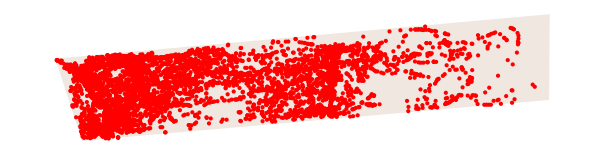

```mathematica
Show[metadataGraphic,Graphics[Style[Point[mergingCoordinates],Red]]]
```

```mathematica
splittingCoordinates=Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@splittingEvents;
```

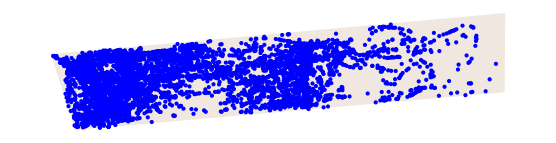

```mathematica
Show[metadataGraphic,Graphics[Style[Point[splittingCoordinates],Blue]]]
```

```mathematica
RegionBounds[paddockRegion]
```

{{580401.,586573.},{6.56269×10^6,6.56428×10^6}}

```mathematica
allCoordinates=Mean[rawCoordinates[[#[[1]],#[[2]]]]]&/@VertexList[FullStabilityGraph]
```

{{580424.,6.56368×10^6},{580431.,6.56368×10^6},1224274,{582275.,6.56363×10^6},{582445.,6.56359×10^6}}
 |  |  |  |

```mathematica
splittingArray=BinCounts[splittingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
mergingArray=BinCounts[mergingCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

```mathematica
allCoordinatesArray=BinCounts[allCoordinates,{580401,586573,50},{6.562693*^6,6.564282*^6,50}];
```

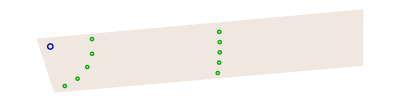

```mathematica
metadataGraphic
```

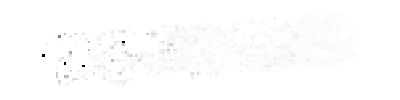

```mathematica
ArrayPlot[Transpose[Quiet[splittingArray/allCoordinatesArray]/.Indeterminate->0],DataReversed->{False,True}]
```

```mathematica
List@@ColorData["TemperatureMap"][10]
```

{0.817319,0.134127,0.164218}

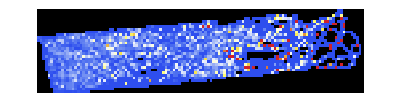

```mathematica
Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[splittingArray/allCoordinatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
}]
```

```mathematica
MeshPrimitives[paddockRegion,1]
```

{Line[{{580735.,6.56269×10^6},{586565.,6.56321×10^6}}],Line[{{586565.,6.56321×10^6},{586573.,6.56428×10^6}}],Line[{{586573.,6.56428×10^6},{580401.,6.56372×10^6}}],Line[{{580401.,6.56372×10^6},{580735.,6.56269×10^6}}]}

```mathematica
Graphics[{Raster[Transpose[Quiet[splittingArray/allCoordinatesArray]]*10,Transpose[RegionBounds[paddockRegion]]],Thick,Red,MeshPrimitives[paddockRegion,1]}]
```

-Graphics-

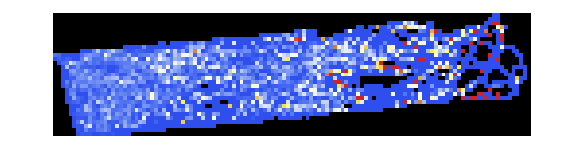

```mathematica
Show[{
metadataGraphic,Graphics[Raster[Map[If[#===Indeterminate,{0,0,0,0},Append[List@@ColorData["TemperatureMap"][#*10],0.8]]&,Transpose[Quiet[mergingArray/allCoordinatesArray]],{2}],Transpose[RegionBounds[paddockRegion]]]]
}]
```